```mathematica
file=FileNameJoin[{NotebookDirectory[],"ms_out.txt"}];
ms=ReadList[file, Number,RecordSeparators->{","}];
sum=Length[ms]
```

100000

```mathematica
sum=1000;
```

```mathematica
Min[ms]
```

0.000993

```mathematica
Max[ms]
```

82.1513

```mathematica
mdensity=BinCounts[ms,0.5]/sum//N;
mdistrib=Accumulate[mdensity];
miicr=(1-mdistrib)/mdensity;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

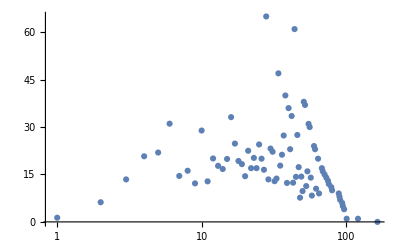

```mathematica
ListLogLinearPlot[miicr]
```

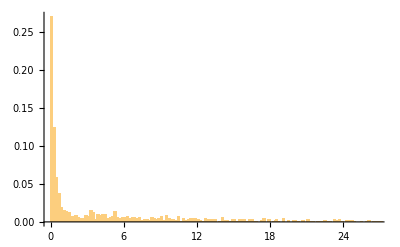

```mathematica
Histogram[ms,300,"Probability"]
```

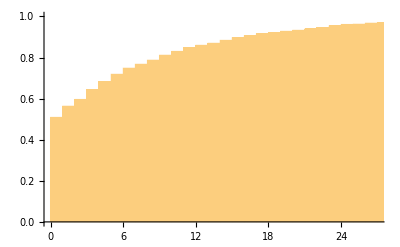

```mathematica
Histogram[ms,100,"CDF"]
```

```mathematica
start=.;
end=.;
n=64;
```

```mathematica
Manipulate[Plot[0.1(Exp[(x Log[1+10end])/n]-1),{x,1,n},PlotRange->All],{start,0,10},{end,0,100}]
```

Plot::plln: Limiting value n in {x,1,n} is not a machine-sized real number.

```mathematica
time = {0,0.001,0.00119708,0.00143301,0.00171543,0.00205352,0.00245824,0.00294272,0.00352269,0.00421696,0.00504806,0.00604296,0.00723394,0.00865964,0.0103663,0.0124093,0.014855,0.0177827,0.0212875,0.0254829,0.0305052,0.0365174,0.0437144,0.0523299,0.0626433,0.0749894,0.0897687,0.107461,0.12864,0.153993,0.184342,0.220673,0.264165,0.316228,0.378552,0.453158,0.542469,0.649382,0.777365,0.930572,1.11397,1.33352,1.59634,1.91095,2.28757,2.73842,3.27812,3.92419,4.69759,5.62341,6.7317,8.05842,9.64662,11.5478,13.8237,16.5482,19.8096,23.7137,28.3874,33.9821,40.6794,48.6968,58.2942,69.7831,83.5363};
```

```mathematica
iicr={0.498002,0.496495,0.511419,0.535112,0.519635,0.527195,0.486053,0.509694,0.501101,0.498992,0.491017,0.509109,0.498356,0.509903,0.504279,0.519946,0.519146,0.518631,0.531167,0.531902,0.533096,0.537593,0.553544,0.55873,0.573439,0.588036,0.6058,0.645052,0.682107,0.720938,0.780971,0.867906,0.985632,1.16129,1.40353,1.80504,2.35394,3.21148,4.36119,5.7959,7.1951,8.30442,8.90559,9.10133,9.02713,8.99482,8.90472,8.83779,8.74464,8.72955,8.6002,8.46783,8.29046,8.22687,7.9838,7.73643,7.40271,7.18653,6.74461,6.26909,5.66484,4.99346,4.67612,4.24731,3.10637};
```

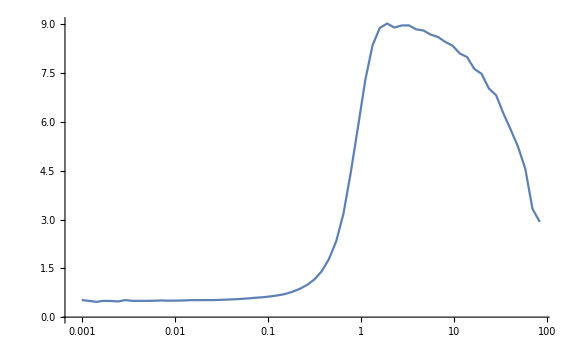

```mathematica
ListLogLinearPlot[Transpose[{time,iicr}],Joined->True,InterpolationOrder->1]
```

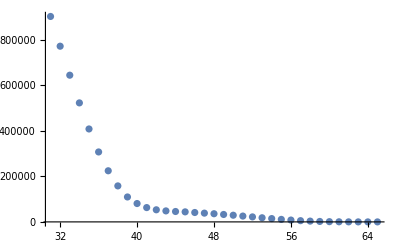

```mathematica
ListPlot[density,PlotRange->All]
```

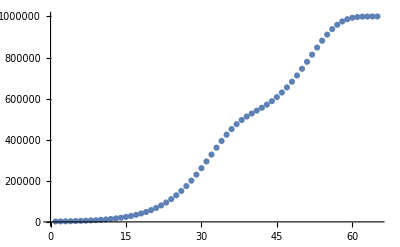

```mathematica
ListPlot[distrib,PlotRange->All]
```

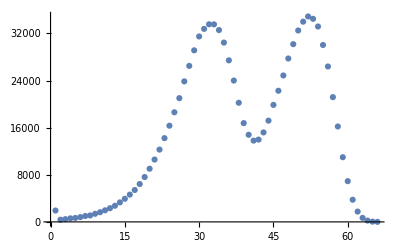

```mathematica
ListPlot[hist,PlotRange->All]
```

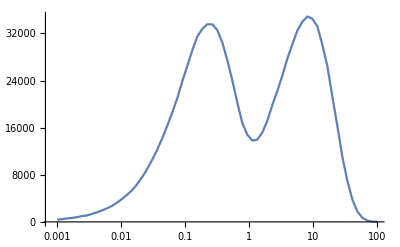

```mathematica
ListLogLinearPlot[Transpose[{Flatten[{time,100}],hist}],Joined->True,InterpolationOrder->1,PlotRange->All]
```

```mathematica
Max[time]
```

83.5363

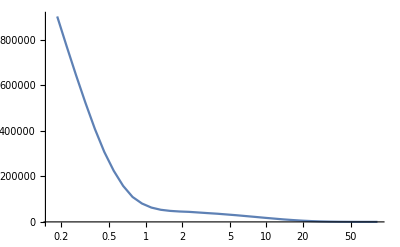

```mathematica
ListLogLinearPlot[Transpose[{time,density}],Joined->True,InterpolationOrder->1,PlotRange->All]
```